# Spacetime Distance

## For x(t)= √(b^2+(ct)^2),if particle gets at x=2b, what is the spacetime distance traversed by it

Solving for t when euclidean distance = 2b, to get bounds of the integral,

```mathematica
Solve[2b-√(b^2+(c*t)^2)==0,t]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t→-(√3 b)/c},{t→(√3 b)/c}}

Taking positive time, t= (√3)/c b,

ds^2/dt^2=-c^2+(dx/dt)^2

```mathematica
x'=D[√(b^2+(c t)^2),t]
```

(c^2 t)/(√(b^2+c^2 t^2))

```mathematica
ds2dt2=-c^2+(x')^2
```

-c^2+(c^4 t^2)/(b^2+c^2 t^2)

Spacetime length= ∫ds/dtdt from t=0 to t=(√3)/c b

```mathematica
dsdt=Sqrt[ds2dt2]
```

√(-c^2+(c^4 t^2)/(b^2+c^2 t^2))

```mathematica
Simplify[dsdt]
```

√(-(b^2 c^2)/(b^2+c^2 t^2))

```mathematica
Integrate[dsdt,{t,0,(√3)/c b}]
```

(b √-c Log[2+√3])/(√c)

```mathematica
FullSimplify[%, c>0]
```

ⅈ b Log[2+√3]

```mathematica
L=ⅈ b Log[2+√3]
```

ⅈ b Log[2+√3]

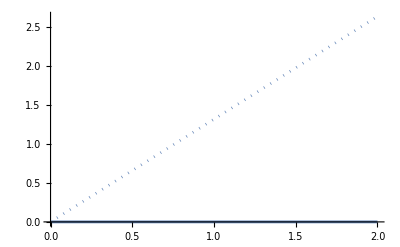

```mathematica
ReImPlot[L,{b,0,2}]
```

Hence, spacetime length between the events for euclidean lengths b and 2b increases linearly as b increases